# Polymer Visualization and Statistical Analysis

## Random Polymers: A Polymer as a Random Walk

### The simplest model of polymer morphology is a sequence of uncorrelated bond lengths. This can be modeled with a random walk.

#### Uncorrelated Random Walk Model of a Polymer

We will fix the bond length to be equal to 2 and visualize the polymers as spheres of radius 1.

Here are two quick examples of visualizing such a random walk with 32 molecular units

```mathematica
steps = AngleVector[{2,#}]&/@RandomReal[{0,2π},32];
positions = Prepend[Accumulate[steps],{0,0}];
Graphics[

]
```

In 3 dimensions, we can use points on a sphere of radius 2 for the step directions

```mathematica
steps = RandomPoint[Sphere[{0,0,0},2],32];
positions = Prepend[Accumulate[steps],{0,0,0}];
Graphics3D[

]
```

#### Expected Length of an Uncorrelated Polymer as a Function of the Number of Units

We can use a Monte Carlo method to generate a set of random walks for a fixed number of units, an then compute the mean of the displacement from the origin of the walk.  Then we can repeat this for different numbers of units.

This function returns the net displacement of an uncorrelated random walk with step lengths of 1

```mathematica
Norm[
Total[ (*net displacement vector*)
RandomPoint[Sphere[],10] (*unit length steps*)
]
]
```

```mathematica
displacement[nUnits_, dimension_/;1<= dimension<= 3]:=
 Norm[
Total[ (*net displacement vector*)
Which[
dimension==1,RandomChoice[{-1,1}],
dimension==2,RandomPoint[Circle[],nUnits],
True,RandomPoint[Sphere[],nUnits]
]
]
]
```

Making sample sizes of 1000 for different numbers of units and computing their means and standard deviations.

```mathematica
displacementData = Table[{2^units,displacement[2^units, 3]},{units,10,18},1000];
(*computation takes about 30 seconds*)
```

```mathematica
meanDisplacements = Mean/@displacementData;
standardDeviationDisplacements = StandardDeviation/@displacementData;
```

```mathematica
Show[
ListPlot[displacementData,],ListLinePlot[MapThread[{#1,Around[#2,#3]}&,{First/@meanDisplacements,Last/@meanDisplacements,Last/@standardDeviationDisplacements}],]
]
```

Let’s see if we can discover the relation between the expected length and number of units

```mathematica
model = a (n)^power;
fit = FindFit[meanDisplacements,model,{a,power},n]
```

```mathematica
fitModel = model/.fit
```

The fit shows that the length increases as 
In our simulation, each If each bond had length = 1.  If the bond length were a, then the results would have been

George, if I had a way to insert “extra stuff, or footnote stuff, I would relate this to diffusion.

```mathematica
probabilityOfAtomPosition3D =Exp[-x^2/(4 diffCoeff t)]/((4 Pi  diffCoeff t )^(3/2))
```

normalized

```mathematica
Integrate[4 Pi x^2  probabilityOfAtomPosition3D,{x,0,Infinity}, Assumptions->diffCoeff> 0 && t> 0]
```

Mean displacement

```mathematica
Integrate[4 Pi x^3  probabilityOfAtomPosition3D,{x,-Infinity,Infinity}, Assumptions->diffCoeff> 0 && t> 0]
```

Mean squared displacement

```mathematica
msqd =Integrate[4 Pi x^4  probabilityOfAtomPosition3D,{x,-Infinity,Infinity}, Assumptions->diffCoeff> 0 && t> 0]
```

```mathematica
Sqrt[msqd/.diffCoeff->1/6]
```

????
 The coefficient seems closer to 1 than .  Does the diffusion equation approximation must over estimate the RMS displacement.  This is reasonable as the derivation produces particles that travel infinitely fast, so there is something in Stirling’s appx that maybe is accounting for this error
 ???

End Footnote

```mathematica
Show[
ListPlot[meanDisplacements,
],
Plot[fitModel,{n,1,10^7}]]
```

Thus, we demonstrate that the expected length polymer with uncorrelated bond direction increases as the square-root of the number of molecular units.

## “Models of Stiff Polymers” Creating a Polymer with Correlations

Some polymers may be less “floppy”: there will be a smaller range of “bending angle” at each molecular unit.
This would create direction correlations in the polymer chain. 

We can model this by creating a correlation in the steps by selecting new directions within a given angle of the previous angle.

In two dimensions, this would be an arc of a circle centered on the previous direction.  In three dimensions, this would be points withing a given solid angle on a sphere.

Two dimensions is  straightforward.  The next direction is chosen from a uniform distribution of angles around the last direction  Δϕ < θ < Δϕ.   AnglePath does exactly this:

```mathematica
Manipulate[
With[{steps = AnglePath[{2,#}&/@RandomReal[{-range/2,range/2},12]]},
Graphics[

]
],
{range,0,2Pi}
]
```

For three dimensions, we need an algorithm to produce random points from a uniform spatial distribution over a spherical cap.

We begin by constructing a formula to find a point on a sphere within a cone aligned with {1,0,0} with a given solid  angle:

```mathematica
Manipulate[
,
{ϕ,0.1,4Pi}
]
```

The red circle above is  intersection of the cone and the sphere. The circle is located at a height z=Cos[ϕ/4] and has a radius r = Sin[ϕ/4].
The probability density of a random point having a radius r is proportional to the circumference of the circle.  The normalized distribution of finding an angle less than α is proportional to:

```mathematica
Integrate[Sin[ϕ/4],{ϕ,0,α}]
```

Normalizing this cumulative probability distribution:

```mathematica
probα=Integrate[Sin[ϕ/4],{ϕ,0,α}]/(8 Sin[αMax/8]^2)
```

Letting a value p be chosen from a uniform 0 < p < 1, then the probability distribution for 0 < α < α_max is

```mathematica
Solve[probα==p,α]
```

This probability method  is employed in another notebook to compute the Partition function of a polymer.  The solid angle scales how many configurations are available and we can associate an energy with the amount of bending.

We can use this result to find a random radius of the circle and its height.  Letting {x,y} be chosen from a uniform distribution on that circle:

```mathematica
randomPointSphericalCap[αMax_]:=Module[{phi =8 ArcSin[Sqrt[RandomReal[{0,1}]]Sin[αMax/8]],r},
r = Sin[phi/4];
Flatten[{Cos[phi/4],r AngleVector[RandomReal[{0,2Pi}]]}]
]
```

```mathematica
randomPointSphericalCap[αMax_,n_]:=Module[{phi =8 ArcSin[Sqrt[RandomReal[{0,1},n]]Sin[αMax/8]],r},
r = Sin[phi/4];
MapThread[
Flatten[{#3,#1 AngleVector[#2]}]&,{r,RandomReal[{0,2Pi},n],Cos[phi/4]}]
]
```

Example

```mathematica
Manipulate[
Graphics3D[Point[randomPointSphericalCap[α,n]]],
{α,0.01,4Pi},
{n,10,2000}
]
```

It will be useful to have a version of this function that returns the rotation matrices the moves a point from {0,0,1} to a random point in the cap of solid angle α_max.

```mathematica
randomPointSphericalCapRotationMatrix[αMax_,n_]:=
Map[
RotationMatrix[{{1,0,0},#}]&,
randomPointSphericalCap[αMax,n]
]
```

```mathematica
MatrixForm/@randomPointSphericalCapRotationMatrix[Pi/6,3]
```

{(0.999167 | 0.0287137 | -0.0289994
-0.0287137 | 0.999588 | 0.000416513
0.0289994 | 0.000416513 | 0.999579),(0.997698 | -0.0255948 | 0.0628053
0.0255948 | 0.999672 | 0.00080467
-0.0628053 | 0.00080467 | 0.998025),(0.998102 | -0.0309314 | 0.0532519
0.0309314 | 0.999521 | 0.000824361
-0.0532519 | 0.000824361 | 0.998581)}

To create this correlated walk, we accumulate vectors that are incrementally rotated.
AnglePath3D does this.
To illustrate, suppose we have a sequence of 20 small rotations around the y-axis:

```mathematica
rotations = Table[RotationMatrix[{{0,0,1},{.1,0,1}}],20];

Graphics3D[Sphere[#,1/2]&/@AnglePath3D[rotations]]
```

-Graphics3D-

```mathematica
Last[AnglePath3D[rotations]]
```

{8.43804,0.,-14.5923}

This is equivalent to a “Folding” a dot-product over the list of rotations:  and then accumulating the vectors in the list:

```mathematica
accumulatedRotations = FoldList[#1.#2&,rotations];
```

```mathematica
steps = #.{1,0,0}&/@accumulatedRotations
```

The only difference is that AngleVector3D prepends a point at {0,0,0}.  This will not be important for our purposes.

```mathematica
Graphics3D[{Opacity[0.2],Blue,Sphere[#,1/2]&/@AnglePath3D[rotations],Red,Opacity[1],Sphere[#,.4]&/@Accumulate[steps]}]
```

-Graphics3D-

```mathematica
Length[Accumulate[steps]]
Length[AnglePath3D[rotations]]
```

The advantage of the Fold method is that:
1) It is much faster:

We can demonstrate that it is faster below for 50000 rotations:

```mathematica
rotations = randomPointSphericalCapRotationMatrix[Pi/4,50000];
```

For AnglePath

In addition to the computation time, we will keep track of the final position to be sure the methods are consistent:

```mathematica
{timingAP,lastPosAP} =RepeatedTiming[Last[pathAP =AnglePath3D[rotations]]]
```

{0.059406,{2034.76,410.247,-1602.42}}

For the fold method:

```mathematica
{timingFP1,lastPosFP1} =RepeatedTiming[Last@Accumulate[pathFP1=(#.{1,0,0})&/@FoldList[Dot[#1,#2]&,rotations]]]
```

{0.015451,{2034.76,410.247,-1602.42}}

Moreover, the Dot product above    picks out the first column of 
Instead of the Dot product, we can grab the column:

```mathematica
{timingFP2,lastPosFP2} =RepeatedTiming[Last@Accumulate[pathFP2=(#[[All,1]])&/@FoldList[Dot[#1,#2]&,rotations]]]
```

{0.0171157,{2034.76,410.247,-1602.42}}

Even better, we can pick out all of the first columns at once:

```mathematica
{timingFP3,lastPosFP3} =RepeatedTiming[Last@Accumulate[pathFP3=(FoldList[Dot[#1,#2]&,rotations][[All,All,1]])]]
```

{0.0113388,{2034.76,410.247,-1602.42}}

We get a speed up of about 5×

```mathematica
timingAP/timingFP3
```

5.31376

If we only need the final point:

```mathematica
{timingFP4,lastPosFP4} =RepeatedTiming[Total[(FoldList[Dot[#1,#2]&,rotations][[All,All,1]])]]
```

{0.0110081,{2034.76,410.247,-1602.42}}

We’ve established the algorithm we should used to embed into functions:

```mathematica
randomCorrelatedWalk[units_, α_]:= 
With[{rotations = 
randomPointSphericalCapRotationMatrix[α,units]},
Accumulate[(FoldList[Dot[#1,#2]&,rotations][[All,All,1]])]
]
```

Or, if we only care about the displacement of the last molecular unit:

```mathematica
randomCorrelatedDisplacement[units_, α_]:= 
With[{rotations = 
randomPointSphericalCapRotationMatrix[α,units]},
Norm[Total[(FoldList[Dot[#1,#2]&,rotations][[All,All,1]])]]
]
```

Visualizing random instances of correlated paths.  We expect that the polymer will be straight/rigid as α becomes small.

```mathematica
Manipulate[
With[{path=randomCorrelatedWalk[units, α]},
Graphics3D[
MapThread[{Hue[#2],Sphere[#1,0.5]}&,{path,0.6 Rescale[Range[Length[path]]]}]
]
],
{α,0.1,4 Pi},
{units,5,1000,1}
]
```

As before, we can do Monte Carlo experiments to find the expected length of a correlated polymer.
We will do repeated experiments for 24 solid angles from {(π,)/6 π/3,(3π)/16,…,4π}.

As we will see below, the computation is time-consuming—which is why we spent some effort above making things faster.

To get a sense of how long each experiment will take:

```mathematica
timingData =Table[{2^units,AbsoluteTiming[randomCorrelatedDisplacement[2^units, Pi/2]]}//Flatten,{units,2,18}]
```

{{4,0.001021,3.89234},{8,0.000763,7.47885},{16,0.001393,14.0693},{32,0.002696,25.2652},{64,0.005276,53.4876},{128,0.011154,62.9944},{256,0.020831,108.893},{512,0.040674,76.6149},{1024,0.082024,143.453},{2048,0.163232,349.248},{4096,0.324992,299.338},{8192,0.661737,269.29},{16384,1.29981,947.064},{32768,2.59217,1961.44},{65536,5.19872,1533.44},{131072,10.5652,1278.79},{262144,21.0918,3560.66}}

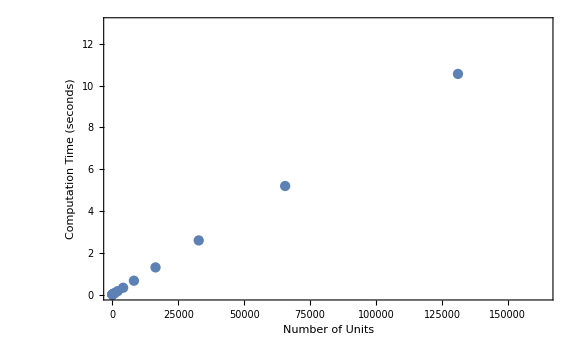

```mathematica
ListPlot[timingData[[All,1;;2]], Frame->True, FrameLabel-> {"Number of Units","Computation Time (seconds)"},ImageSize->Large, BaseStyle->18]
```

The total time we need to do 1 experiment for up to 262144 units is about one minute:

```mathematica
totalTime= Total[timingData[[All,2]]]
```

42.0635

If we do all the angles in parallel for 2^2 to 2^16 units (i.e., ParallelTable) it takes about 1 minute (8 CPUs)

```mathematica
AbsoluteTiming[result=
ParallelTable[
Table[α->{2^units,randomCorrelatedDisplacement[2^units, α]},{units,2,16}],
{α,Pi/6,4Pi,Pi/6}
];
]
```

{55.7134,Null}

Supposing we had enough patience to wait  1 hour, we could only do 15 repeated experiments.  This is likely insufficient for good statistics.

Another approach would be to do a single experiment for a large number of units, and then use the data from smaller subsequences of steps from that data.   This would produce correlations in the data, so it is not ideal.

To do a single experiment in parallel, this method takes about 1/2 as long:

```mathematica
AbsoluteTiming[
result =ParallelTable[
α->Association[With[{walkExperiment =
randomCorrelatedWalk[2^16, Pi/2]
},
Association@Table[
2^n-><|
"Mean"->Mean[Norm/@walkExperiment[[n]]],"Standard Deviation"-> StandardDeviation[Norm/@walkExperiment[[n]]]
|>,{n,1,16}]
]],
{α,Pi/6,4Pi,Pi/6}
];
]
```

{27.9883,Null}

So, if our patience limit is 1 hour, we would do  120 Monte Carlo repetitions.
Can you  find something interesting or fun (optimally both) to do for 5 minutes and let it run for 10?

```mathematica
AbsoluteTiming[
With[{monteCarloExperiments =10, nExponent=16},
correlatedRandomWalkData =
Join[<|"Monte Carlo Experiments"->monteCarloExperiments|>, Association[
ParallelTable[
(*Print[{α,DateString[]}];*)
<|α->
With[{walkExperiments =
Table[randomCorrelatedWalk[2^nExponent, α],monteCarloExperiments]
},
Association@Table[
2^n-><|
"Mean"->Mean[Norm/@walkExperiments[[All,2^n]]],"Standard Deviation"-> StandardDeviation[Norm/@walkExperiments[[All,2^n]]],
"Mean Direction"->Mean[walkExperiments[[All,2^n]]-walkExperiments[[All,2^n -1]] ]|>,
{n,1,nExponent}]
]|>,
{α,Pi/6,4Pi,Pi/6}
]
]
];
]
]
```

Or, if you don' t want to wait .  We' ve done a 4 hour run  (500 experiments, up to 2^16 molecular units) and saved the data with “CloudSave”

You can grab that data as follows:

```mathematica
(*cloudData =CloudSave[correlatedRandomWalkData,"correlatedRandomWalkData_n=500_exp=16"]*)
```

```mathematica
CloudGet[CloudObject[["https://www.wolframcloud.com/obj/ccarter/correlatedRandomWalkData_n=500_exp=16"](https://www.wolframcloud.com/obj/ccarter/correlatedRandomWalkData_n=500_exp=16)]
]
```

The data is arranged as follows:

```mathematica
Keys[correlatedRandomWalkData]
```

{Monte Carlo Experiments,π/6,π/3,π/2,(2 π)/3,(5 π)/6,π,(7 π)/6,(4 π)/3,(3 π)/2,(5 π)/3,(11 π)/6,2 π,(13 π)/6,(7 π)/3,(5 π)/2,(8 π)/3,(17 π)/6,3 π,(19 π)/6,(10 π)/3,(7 π)/2,(11 π)/3,(23 π)/6,4 π}

```mathematica
correlatedRandomWalkData["Monte Carlo Experiments"]
```

500

```mathematica
correlatedRandomWalkData[Pi/6]
```

<|2→<|Mean→1.99778,Standard Deviation→0.00120223,Mean Direction→{0.990563,0.00320579,-0.00249225}|>,4→<|Mean→3.98931,Standard Deviation→0.00582801,Mean Direction→{0.98226,0.00263634,0.00334511}|>,8→<|Mean→7.95674,Standard Deviation→0.0240641,Mean Direction→{0.968405,0.00293189,0.00431901}|>,16→<|Mean→15.8246,Standard Deviation→0.103086,Mean Direction→{0.934927,-0.0038825,-0.00674156}|>,32→<|Mean→31.2807,Standard Deviation→0.39618,Mean Direction→{0.870697,-0.00335256,-0.0225608}|>,64→<|Mean→61.1733,Standard Deviation→1.63917,Mean Direction→{0.7559,-0.00800596,-0.00149078}|>,128→<|Mean→117.044,Standard Deviation→6.4282,Mean Direction→{0.57567,0.00931307,-0.00868981}|>,256→<|Mean→215.88,Standard Deviation→21.5407,Mean Direction→{0.357355,0.0313897,-0.0257347}|>,512→<|Mean→368.043,Standard Deviation→69.9456,Mean Direction→{0.105569,-0.00711773,0.0135144}|>,1024→<|Mean→581.899,Standard Deviation→172.182,Mean Direction→{-0.0138613,-0.0152171,0.00778843}|>,2048→<|Mean→871.575,Standard Deviation→300.667,Mean Direction→{-0.0248078,-0.032458,0.00806274}|>,4096→<|Mean→1245.73,Standard Deviation→490.264,Mean Direction→{0.0145783,0.0667842,-0.0385165}|>,8192→<|Mean→1764.89,Standard Deviation→725.714,Mean Direction→{-0.0367318,0.0435576,-0.0417145}|>,16384→<|Mean→2492.52,Standard Deviation→1074.4,Mean Direction→{-0.00796142,-0.00243262,0.0239781}|>,32768→<|Mean→3524.46,Standard Deviation→1528.88,Mean Direction→{0.0126251,-0.0521419,-0.0036556}|>,65536→<|Mean→5012.78,Standard Deviation→2181.13,Mean Direction→{-0.0700098,0.0306537,-0.0298671}|>|>

```mathematica
correlatedRandomWalkData[Pi/6][[All,"Mean"]]
```

<|2→1.99778,4→3.98931,8→7.95674,16→15.8246,32→31.2807,64→61.1733,128→117.044,256→215.88,512→368.043,1024→581.899,2048→871.575,4096→1245.73,8192→1764.89,16384→2492.52,32768→3524.46,65536→5012.78|>

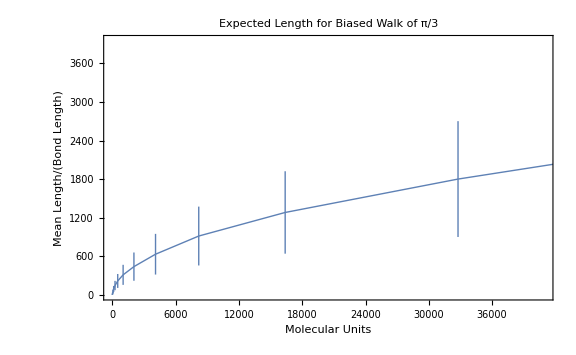

```mathematica
With[{means = correlatedRandomWalkData[Pi/3][[All,"Mean"]],
deviations = correlatedRandomWalkData[Pi/3][[All,"Mean"]]},
ListLinePlot[
MapThread[Around[#1,#2]&,{means,deviations/2}],Frame->True,FrameLabel->{"Molecular Units","Mean Length/(Bond Length)"},ImageSize->Large,BaseStyle->{FontSize->18,Thick},PlotLabel->"Expected Length for Biased Walk of π/3"]
]
```

Writing a function to extract the data for a subsequent visualization:

```mathematica
correlatedRandomWalkPlotData[randomWalkData_,α_]:=
MapThread[Around[#1,#2/2]&,{randomWalkData[α][[All,"Mean"]],randomWalkData[α][[All,"Standard Deviation"]]}
]
```

```mathematica
correlatedRandomWalkPlotData[correlatedRandomWalkData,Pi/6]
```

<|2→1.99780.0006,4→3.98930.0029,8→7.9570.012,16→15.820.05,32→31.280.20,64→61.20.8,128→117.03.2,256→216.11.,512→368.35.,1024→582.86.,2048→872.150.,4096→1246.245.,8192→1765.363.,16384→2493.537.,32768→3524.764.,65536→5.01.110^3|>

```mathematica
DynamicModule[

]
```

If the solid angle α = 0, then we would expect the length to grow linearly with the number of units because the polymer would be straight.
How does the fit we found above   change with α?

We have to rearrange the data into a list:

```mathematica
With[{keys =Keys[correlatedRandomWalkData[Pi/6]], values =Values [correlatedRandomWalkData[Pi/6][[All,"Mean"]]]},
Transpose[{keys, values}]
]
```

```mathematica
model = a + b n^p
```

a+b n^p

Even for highly correlated bond angles, the expected length scales as :

```mathematica
FindFit[With[{keys =Keys[correlatedRandomWalkData[Pi/6]], values =Values [correlatedRandomWalkData[Pi/6][[All,"Mean"]]]},
Transpose[{keys, values}]
],
model, {a,b,p},n]
```

{a→-71.7286,b→21.2499,p→0.493902}

However, if we look at  limited range of data, we can see that the power law exponent shifts from 1 to 1/2.  That is, the polymer morphology has a “correlation length”

We also kept data for the mean of the last bond direction:

```mathematica
correlatedRandomWalkData[Pi/6][[All,"Mean Direction"]]
```

<|2→{0.990563,0.00320579,-0.00249225},4→{0.98226,0.00263634,0.00334511},8→{0.968405,0.00293189,0.00431901},16→{0.934927,-0.0038825,-0.00674156},32→{0.870697,-0.00335256,-0.0225608},64→{0.7559,-0.00800596,-0.00149078},128→{0.57567,0.00931307,-0.00868981},256→{0.357355,0.0313897,-0.0257347},512→{0.105569,-0.00711773,0.0135144},1024→{-0.0138613,-0.0152171,0.00778843},2048→{-0.0248078,-0.032458,0.00806274},4096→{0.0145783,0.0667842,-0.0385165},8192→{-0.0367318,0.0435576,-0.0417145},16384→{-0.00796142,-0.00243262,0.0239781},32768→{0.0126251,-0.0521419,-0.0036556},65536→{-0.0700098,0.0306537,-0.0298671}|>

Because the first step is always {1,0,0}, the first component of the mean direction is a measure of the correlation to the first bond.
For α = π/6, the correlation disappears after about 1000 units.

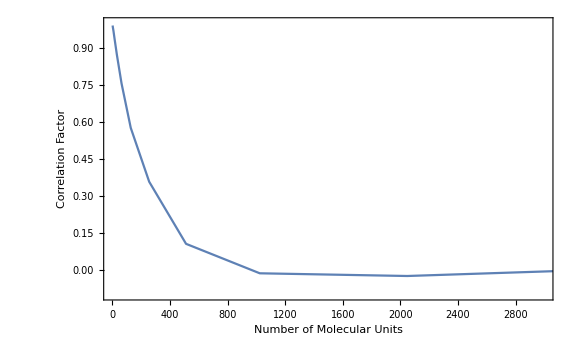

```mathematica
ListLinePlot[First/@correlatedRandomWalkData[Pi/6][[All,"Mean Direction"]],
]
```

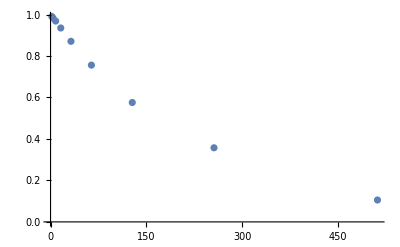

```mathematica
limitedData =With[{keys =Keys[correlatedRandomWalkData[Pi/6]], values =First/@Values [correlatedRandomWalkData[Pi/6][[All,"Mean Direction"]]]},
Transpose[{keys, values}][[1;;9]]
];
limitedDataPlot =ListPlot[limitedData]
```

```mathematica
correlationModel = Exp[-n/η];
correlationFit =FindFit[limitData,correlationModel,η,n]
```

{η→237.035}

The characteristic correlation length is about 240 units

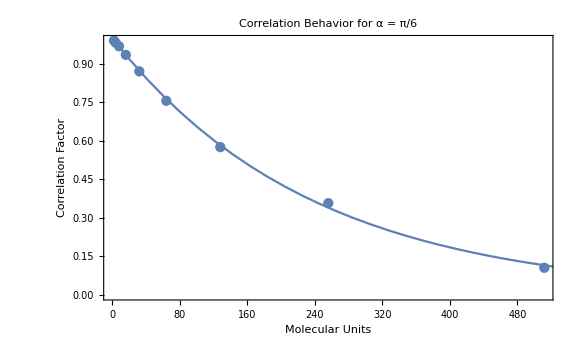

```mathematica
Show[ListPlot[limitData],Plot[correlationModel/.correlationFit,{n,0,1000}],ImageSize->Large,Frame->True, FrameLabel-> {"Molecular Units","Correlation Factor"},
PlotLabel->"Correlation Behavior for α = π/6", BaseStyle->{FontSize->16}]
```

For α = 2π (i.e., the polymer never “bends backwards” )
The  correlation has effectively vanished after 3 about steps.

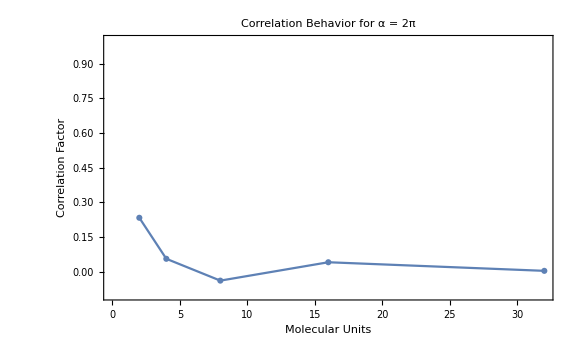

```mathematica
ListLinePlot[]
```

If we look at the behavior of a single polymer with α=π/6:

```mathematica
path= randomCorrelatedWalk[1000, Pi/3];
Graphics3D[Tube[path]]
```

-Graphics3D-

We can see that the correlation is a random walk on a sphere where the step size is the solid angle α

```mathematica
Graphics3D[Tube[Differences@path]]
```

-Graphics3D-